{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

no. | title | length
1 | cpu_time | 417
2 | eq_of_motion | 417
3 | float_COM | 417
4 | float_EK | 417
5 | float_EP | 417
6 | float_accel | 417
7 | float_area | 417
8 | float_drag_force | 417
9 | float_drag_torque | 417
10 | float_force | 417
11 | float_pitch | 417
12 | float_roll | 417
13 | float_torque | 417
14 | float_velocity | 417
15 | float_yaw | 417
16 | gradPhi_worst_grad | 417
17 | gradPhi_worst_iteration | 417
18 | gradPhi_worst_value | 417
19 | simulation_time | 417
20 | wall_clock_time | 417
21 | water_E | 417
22 | water_EK | 417
23 | water_EP | 417
24 | water_face_size | 417
25 | water_point_size | 417
26 | water_volume | 417

1.93625

6.45578

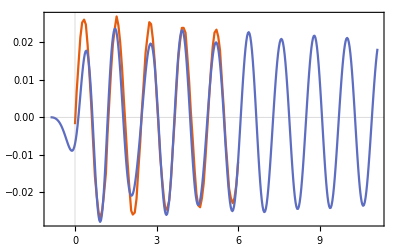

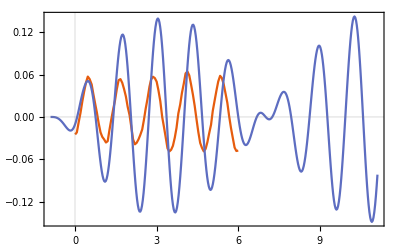

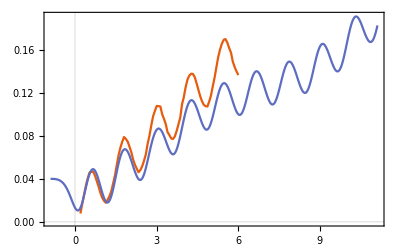

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
filename="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_DT0d03_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json";
jsonInfo[filename]
data=Import[filename];

d=0.4;
T=1.2;
k=getkFromTandDepth[T,d];
L=2π/k
c=L*T;
15/c
shift=0.9;

dataHeave=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_heave.csv"}]];
ListPlot[{{T*#1,d*#2}&@@@dataHeave,Transpose[{("simulation_time"/.data)-shift,("float_COM"/.data)[[;;,3]]-0.4}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataPitch=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_pitch.csv"}]];
ListPlot[{{T*#1,d*k*#2}&@@@dataPitch,Transpose[{("simulation_time"/.data)-shift,("float_pitch"/.data)}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataSurge=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_surge.csv"}]];
ListPlot[{{T*#1,d*#2}&@@@dataSurge,Transpose[{("simulation_time"/.data)-shift,0.04+("float_COM"/.data)[[;;,1]]}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

1.93625

6.45578

{/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d6_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d65_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d7_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d75_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d8_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d85_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d9_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d95_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json}

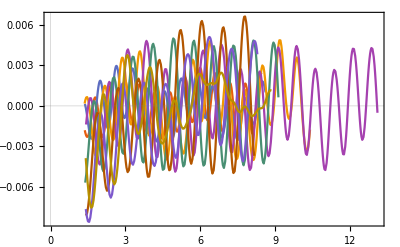

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

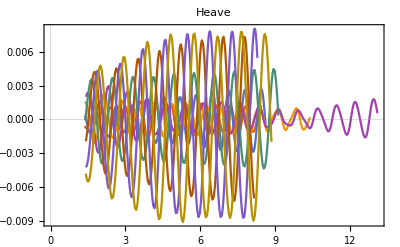

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

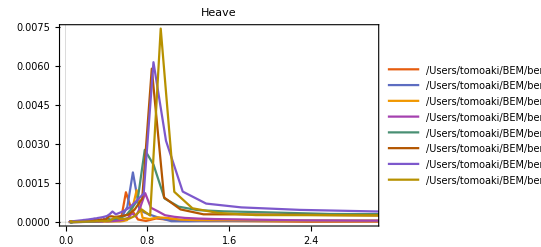

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

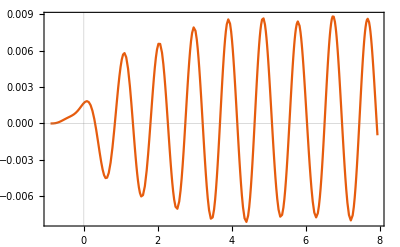

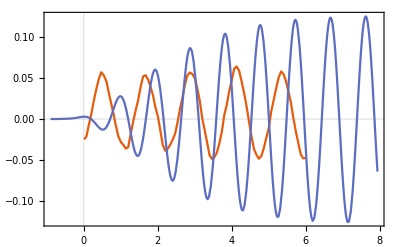

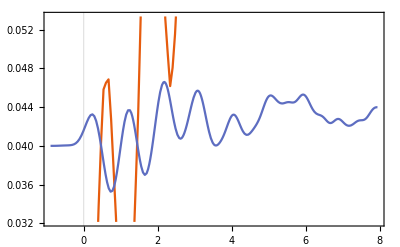

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]

d=0.4;
T=1.2;
k=getkFromTandDepth[T,d];
L=2π/k
c=L*T;
15/c
shift=0.9;

Ts={0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95};
filenames={
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d6_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d65_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d7_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d75_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d8_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d85_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d9_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",
"/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d95_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json"
}

start=30;

DATA=Table[data=Import[name];Transpose[{("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,1]]-Mean[("float_COM"/.data)[[start;;,1]]]}],{name,filenames}];
ListPlot[DATA,Evaluate[plot2Doption]]

DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,1]]-Mean[("float_COM"/.data)[[start;;,1]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA,PlotRange->All,PlotLegends->filenames]

DATA=Table[data=Import[name];Transpose[{("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]}],{name,filenames}];
ListPlot[DATA,Evaluate[plot2Doption]
,PlotLabel->"Heave"]

DATA=Table[data=Import[name];{1/#1,#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]],{name,filenames}];
ListPlot[DATA,PlotRange->{{0,3},All}
,PlotRange->All,Evaluate[plot2Doption]
,PlotLegends->filenames
,PlotLabel->"Heave"]

DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA
,PlotRange->All
,PlotLegends->filenames
,PlotLabel->"Heave"]


DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_pitch"/.data)[[start;;]]-Mean[("float_pitch"/.data)[[start;;]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA
,PlotRange->All
,PlotLegends->filenames
,PlotLabel->"Pitch"]

dataHeave=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_heave.csv"}]];
ListPlot[{(*{T*#1,d*#2}&@@@dataHeave,*)Transpose[{("simulation_time"/.data)-shift,("float_COM"/.data)[[;;,3]]-(1-0.097+0.091)}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataPitch=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_pitch.csv"}]];
ListPlot[{{T*#1,d*k*#2}&@@@dataPitch,Transpose[{("simulation_time"/.data)-shift,("float_pitch"/.data)}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataSurge=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_surge.csv"}]];
ListPlot[{{T*#1,d*#2}&@@@dataSurge,Transpose[{("simulation_time"/.data)-shift,0.04+("float_COM"/.data)[[;;,1]]}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
```

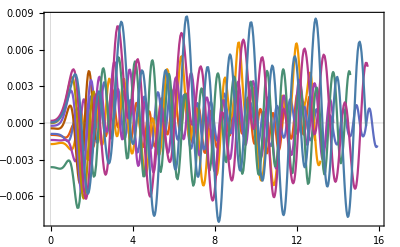

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

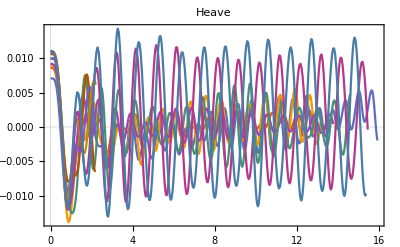

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

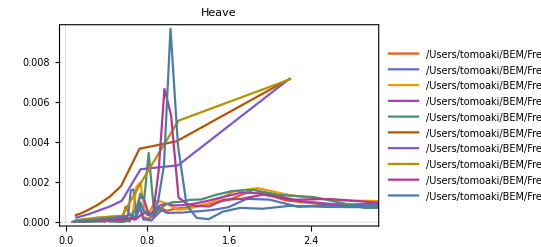

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-